### Expressions

Everything in the Wolfram Language is an expression

head[arg_1,arg_2,...,arg_n]

arg_1 : head_1[arg_(1,1),arg_(1,2),...,arg_(1,n_1)]

arg_2: head_2[arg_(2,1), arg_(2,2),...,arg_(2,n_2)]

⋮

arg_n: head_2[arg_(n,1), arg_(n,2),...,arg_(n,n_n)]

#### Atomic Elements

Atomic Elements or Atomic Expressions can be though of as the basic types of elements in the Wolfram Language. They include

Integer

```mathematica
{1,2,3,4,-1,-2,-3,..}
```

Real

```mathematica
{3.4,2.0,9.123456,...}
```

String

```mathematica
{"Hello","Welcome to day 2 of the Wolfram Workshop!", "xadsasvasd",...}
```

Rational

```mathematica
{1/2,3/4,4/5,16/3,...}
```

Symbol

```mathematica
{x, Pi, π, hello, Plot,...}
```

We can identify which constructs are atoms by using the AtomQ function.

```mathematica
(*Examples*){AtomQ[1],AtomQ[3.4],AtomQ["Hello"],AtomQ[1/2],AtomQ[x]}
```

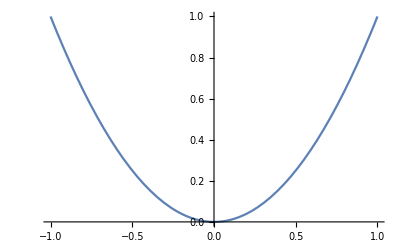
```mathematica
(*Non-Examples*){AtomQ[2x],AtomQ[5 x^2+6x+1==0],AtomQ[{1,2,3}],AtomQ[LinguisticAssistant],AtomQ[-Graphics-]}
```

This tells you that these last expressions are something more complicated (we will get to that later).

We can tell what “type” of atomic elements we have by using the Head function.

```mathematica
{Head[1],Head[3.4],Head["Hello"],Head[1/2],Head[x]}
```

#### More complex expressions

What about the non-atomic expressions that we had before?

We can still take the Head of any expression.

```mathematica
{Head[2x],Head[5 x^2+6x+1==0],Head[{1,2,3}],Head[LinguisticAssistant],Head[-Graphics-]}
```

Even though they look all different, internally they all have the same structure, that comes from language design principles in logic. That is, they all have the form:

head[argument1, argument2,...]

where the heads are Times, Equal, List, Entity, and Graphics respectively, and each argument could be either another complex expression or an atomic element.

We can see in detail how these expressions are understood by the software using the FullForm function

```mathematica
FullForm[2x]
```

```mathematica
FullForm[5 x^2+6x+1==0]
```

```mathematica
FullForm[{1,2,3}]
```

```mathematica
FullForm[LinguisticAssistant]
```

```mathematica
FullForm[-Graphics-]
```

```mathematica
{TreeForm[2x],TreeForm[5 x^2+6x+1==0],TreeForm[{1,2,3}],TreeForm[LinguisticAssistant]}
```

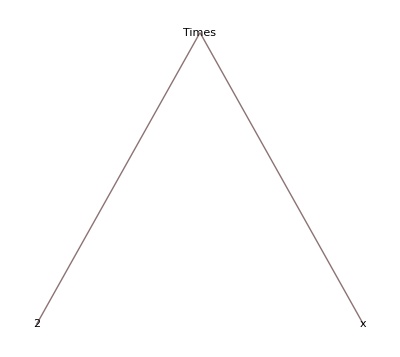
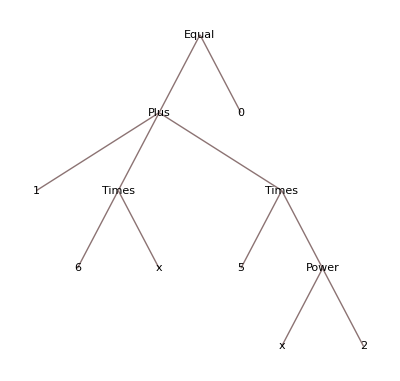
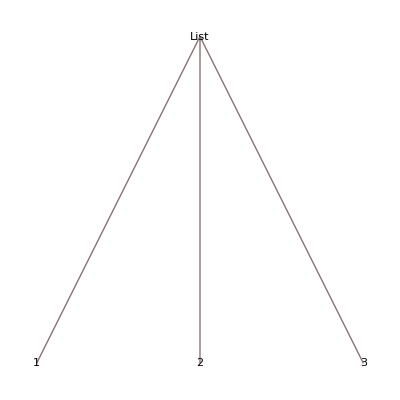
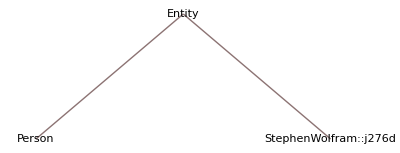

#### An Important Observation about Head

Even though Head gives you the type of element we are working with, it should not be confused with the Function that led to its creation.

```mathematica
{Table[i,{i,5}],Range[5],List[1,2,3,4,5],Map[Length,{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}]}
```

```mathematica
Head/@%
```

#### Why is understanding expressions important

Everything is an expression

The notebook I am presenting with, the cells, and the code itself are all expressions

To understand the language and different constructs as they appear.

Knowing that there is a carefully thought structuring of the language helps you get familiar with new functionality as you run into it.

To be able to read code from others(and eventually modify it for your own purposes)

Even though there is a standard form (FullForm) of expressions there are different ways in which code can be input.

f@a

a//f

f[a]

#### Functions that work with all Expressions

Head

Head[atomic] gives you the type of atomic element.

head[f[e1,e2,...,en]] gives you f.

Length

Length of an atomic element gives you 0.

```mathematica
Length["Hello there"]
```

Length  of f[e1,e2,..en] gives you n.

```mathematica
Length[{1,2,3,4}]
```

```mathematica
Length[a+2x y]
```

```mathematica
Length[If[a<b,"x","y"]]
```

Part

Part[expr,0] is the same as taking Head[expr]

Part[f[e1,e2,...,en],k] is the same as ek.

We usually use the shorthand expr[[k]] for Part[expr,k]

```mathematica
{1,2,3,4}[[2]]
```

```mathematica
{1,2,3,4}[[0]]
```

```mathematica
3[[0]]
```

```mathematica
x[[0]]
```

```mathematica
x[[1]]
```

```mathematica
{1,2,3,4}[[5]]
```

```mathematica
a+b[[2]]
```

```mathematica
(a+b)[[2]]
```

### Exercises Set 1

Which of the following general Elements are atomic?

String

Built-in Symbol

Entity

Integer

Real

List

Rational

Symbol

For the following questions consider the following 9 expressions

```mathematica
Grid[Partition[{5,{1,2},m,Select,x+3,"\"{1,2,3}\"",HoldForm[1+7],Log[7],HoldForm[Log[7.]]},3],Frame->All]
```

Which expressions are atomic?

|   |  
  |   |  
  |   |

What are the heads of the expressions?

|   |  
  |   |  
  |   |

Can the second Part of an expression be a List?

Can the second argument of the function Part be a list?